```mathematica
A=0.9
```

0.9

```mathematica
B=0.65
```

0.65

```mathematica
eqns1=x'[t]==A+x[t]^2*y[t]-(B+1)*x[t]
```

x'[t]==0.9-1.65 x[t]+x[t]^2 y[t]

```mathematica
eqn2=y'[t]==B*x[t]-x[t]^2*y[t]
```

y'[t]==0.65 x[t]-x[t]^2 y[t]

```mathematica
ics1 = x[0]==0.5
```

x[0]==0.5

```mathematica
ics2=y[0]==0.8
```

y[0]==0.8

```mathematica
sol= NDSolve[{eqns1, eqn2,ics1, ics2}, {x[t],y[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t],y[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

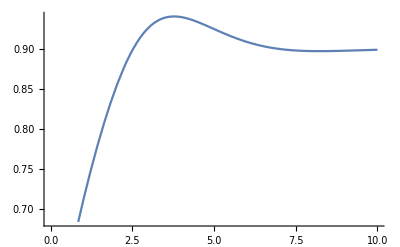

```mathematica
Plot[Evaluate[x[t]/.sol], {t,0,10}]
```

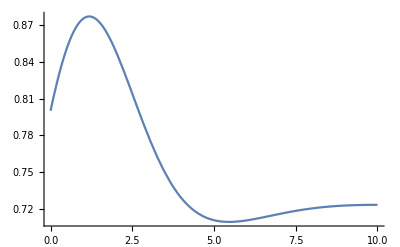

```mathematica
Plot[Evaluate[y[t]/.sol],{t,0,10}]
```

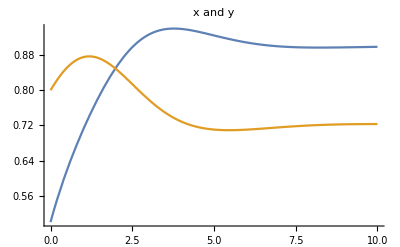

```mathematica
Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}, PlotLabel->"x and y"]
```

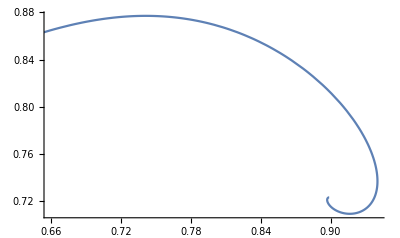

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,10}]
```